```mathematica
(*Constants*)
```

```mathematica
χ=3.1*10^(-4);
OmegaM=0.3153;
OmegaR=OmegaM*χ;
OmegaL=0.681369;
H0=1.37187*10^(-33);
ms=1.37201*10^(-67);
sqrms=N[ Sqrt[ms],10];
Λ=11.895*10^(-67);
zfin=10;
b=1;
r=Λ/(3*ms)*(1+(zfin+1)/1000);
φ=Λ/(3*ms)*1/1000;
M=3.04375×1022;
```

```mathematica
viable = Import["C:\\Users\\grega\\Documents\\viable-ns-parameters-emergent-universe.mx"]
```

{{50.,0.433333,14.8667,14.4667,1},{50.,0.433333,14.8667,14.4667,1},{50.,0.433333,14.8667,14.4667,1},{50.,0.433333,14.8667,14.4667,1},1880,{60.,0.6,14.6,14.5333,1},{60.,0.6,14.6,14.5333,1},{60.,0.6,14.6,14.5333,1},{60.,0.6,14.6,14.5333,1}}
 |  |  |  |

```mathematica
(*Basic functions*)
a[z_]:=1/(1+z)
rs[z_]:=a[z]^(-4)*(χ);
R[z_]:=3*ms*((-1/a[z])*y'[z]+4 y[z]+a[z]^(-3));
```

```mathematica
a[z]
```

1/(1+z)

```mathematica
(*The gravity model*)
F[R_]
```

c1 ⅇ^(1/2 ((k^2 p^2 (-55+54 √2+18 p^2+9 √2 (1-6 p^2)))/(34992-40824 √2-34992 (-1+4 p^2)+324 √2 (-17+378 p^2)+(1-18 p^2)^2 (-1+108 p^4)+216 (-5-342 p^2+972 p^4)-54 √2 (-13-132 p^2+2268 p^4)-12 (19-108 p^2-3564 p^4+11664 p^6)+√2 (17-342 p^2-1620 p^4+40824 p^6))-√((k^4 p^4 (209952-244944 √2-5832 (-37+144 p^2)+3888 √2 (-10+189 p^2)+(1-18 p^2)^2 (-5+648 p^4)+324 (-5-1404 p^2+3888 p^4)-108 √2 (-29-468 p^2+6804 p^4)+12 √2 (7-135 p^2-972 p^4+20412 p^6)-18 (61-216 p^2-14580 p^4+46656 p^6)))/((-34992+40824 √2+34992 (-1+4 p^2)-324 √2 (-17+378 p^2)-(1-18 p^2)^2 (-1+108 p^4)-216 (-5-342 p^2+972 p^4)+54 √2 (-13-132 p^2+2268 p^4)+√2 (-17+342 p^2+1620 p^4-40824 p^6)+12 (19-108 p^2-3564 p^4+11664 p^6))^2))) R_)-c1 ⅇ^(1/2 ((k^2 p^2 (-55+54 √2+18 p^2+9 √2 (1-6 p^2)))/(34992-40824 √2-34992 (-1+4 p^2)+324 √2 (-17+378 p^2)+(1-18 p^2)^2 (-1+108 p^4)+216 (-5-342 p^2+972 p^4)-54 √2 (-13-132 p^2+2268 p^4)-12 (19-108 p^2-3564 p^4+11664 p^6)+√2 (17-342 p^2-1620 p^4+40824 p^6))+√((k^4 p^4 (209952-244944 √2-5832 (-37+144 p^2)+3888 √2 (-10+189 p^2)+(1-18 p^2)^2 (-5+648 p^4)+324 (-5-1404 p^2+3888 p^4)-108 √2 (-29-468 p^2+6804 p^4)+12 √2 (7-135 p^2-972 p^4+20412 p^6)-18 (61-216 p^2-14580 p^4+46656 p^6)))/((-34992+40824 √2+34992 (-1+4 p^2)-324 √2 (-17+378 p^2)-(1-18 p^2)^2 (-1+108 p^4)-216 (-5-342 p^2+972 p^4)+54 √2 (-13-132 p^2+2268 p^4)+√2 (-17+342 p^2+1620 p^4-40824 p^6)+12 (19-108 p^2-3564 p^4+11664 p^6))^2))) R_)

```mathematica
f[R_] = F[R]-R;
```

```mathematica
(*Redshift DE*)
```

```mathematica
J1[z_]:=a[z]*(-3-1/(y[z]+a[z]^(-3)+rs[z])*(1-f'[R[z]])/(6*ms*f''[R[z]]))
J2[z_]:=(a[z]^2)*(1/(y[z]+a[z]^(-3)+rs[z]))*(2-f'[R[z]])/(3*ms*f''[R[z]])
J3[z_]:=-3*a[z]^(-1)-(a[z]^2)*((1-f'[R[z]])*(a[z]^(-3)+2rs[z])+(R[z]-f[R[z]])/(3*ms))/(6*ms*f''[R[z]])
```

```mathematica
(*Inserting the viable n and c1 parameters*)
```

```mathematica
lateviable =ParallelMap[{#[[2]],#[[4]],#[[5]]}&,viable];
```

```mathematica
resolutionparameter = 1;
clearedviable = {};
For[i=1,i<=Length[lateviable],i++, If[Mod[i,resolutionparameter]==0, clearedviable=AppendTo[clearedviable, lateviable[[i]]]]]
```

```mathematica
clearedviable;
Length[clearedviable]
```

1888

```mathematica
(*The sol of the DE*)
acc = 0.001;
soly={};
solyExtended={};
incond = {};
lim=Length[clearedviable];
conprint = Floor[lim/10]; (*Thay way only 10 messages shall be printed *)

Quiet[For[i=1,i<=lim,i++,{k,p,c1}=clearedviable[[i]];
AppendTo[soly,NDSolve[{y''[z]+J1[z]*y'[z]+J2[z]*y[z]+J3[z]==0,y[zfin]==r,y'[zfin]==φ},y,{z,0,zfin+0.1},Method->"LSODA",MaxStepSize->acc,WorkingPrecision->30,InterpolationOrder->All]];
AppendTo[incond,{y[0.1]/. soly[[i,1]],y'[0.1]/. soly[[i,1]]}];
If[Mod[i,conprint]==0,Print["The process of constructing an interpolation function for values at [0,10] is at ",N[(100*i/lim),3],"%"]];]];
soly=Flatten[soly];
incond;
```

The process of constructing an interpolation function for values at [0,10] is at 9.96%

The process of constructing an interpolation function for values at [0,10] is at 19.9%

The process of constructing an interpolation function for values at [0,10] is at 29.9%

The process of constructing an interpolation function for values at [0,10] is at 39.8%

The process of constructing an interpolation function for values at [0,10] is at 49.8%

The process of constructing an interpolation function for values at [0,10] is at 59.7%

The process of constructing an interpolation function for values at [0,10] is at 69.7%

The process of constructing an interpolation function for values at [0,10] is at 79.7%

The process of constructing an interpolation function for values at [0,10] is at 89.6%

The process of constructing an interpolation function for values at [0,10] is at 99.6%

```mathematica
Clear[y]
ClearAll
```

ClearAll

```mathematica
Quiet[For[i=1,i<=lim,i++,{k,p,c1}=clearedviable[[i]];
AppendTo[solyExtended,NDSolve[{y''[z]+J1[z]*y'[z]+J2[z]*y[z]+J3[z]==0,y[0.1]==incond[[i,1]],y'[0.1]==incond[[i,2]]},y,{z,-0.1,0.1},Method->"LSODA",MaxStepSize->acc,WorkingPrecision->30,InterpolationOrder->All]];
If[Mod[i,conprint]==0,Print["The process of extending the interpolation at values near zero is at ",N[(100*i/lim),3],"%"]];];
solyExtended=Flatten[solyExtended];
If[Length[soly]==Length[solyExtended],Print["The code was successfull"]]]
```

The process of extending the interpolation at values near zero is at 9.96%

The process of extending the interpolation at values near zero is at 19.9%

The process of extending the interpolation at values near zero is at 29.9%

The process of extending the interpolation at values near zero is at 39.8%

The process of extending the interpolation at values near zero is at 49.8%

The process of extending the interpolation at values near zero is at 59.7%

The process of extending the interpolation at values near zero is at 69.7%

The process of extending the interpolation at values near zero is at 79.7%

The process of extending the interpolation at values near zero is at 89.6%

The process of extending the interpolation at values near zero is at 99.6%

The code was successfull

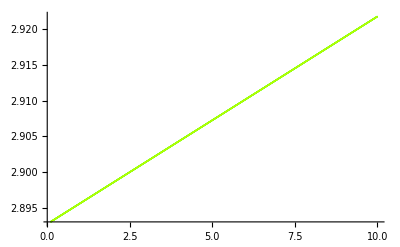

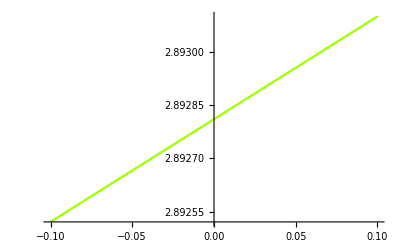

```mathematica
Clear[plots,plotsextended];
plots=Table[Plot[y[z]/.soly[[i]],{z,0.1,10},PlotStyle->{Thick,RGBColor[0.1*i,1,0]}],{i,Floor[Length[soly]/250]}];
plotsextended=Table[Plot[y[z]/.solyExtended[[i]],{z,-0.1,0.1},PlotStyle->{Thick,RGBColor[0.1*i,1,0]}],{i,Floor[Length[soly]/250]}];
Show[plots]
Show[plotsextended]
(*If the two graphs exist and the point of change seems continuous , all went well*)
```

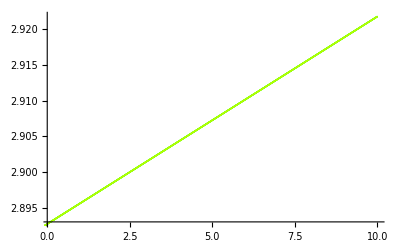

```mathematica
Show[plots,plotsextended,FrameLabel->{"z","y[z]"}]
```

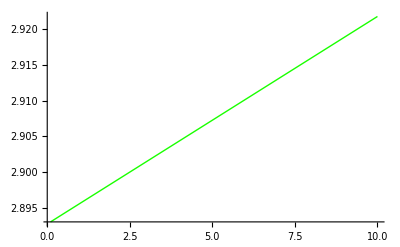
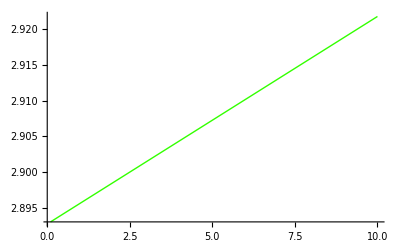
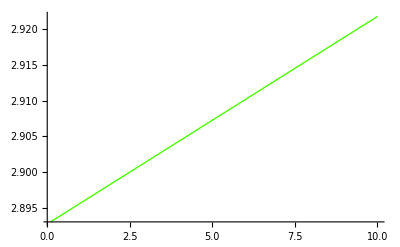
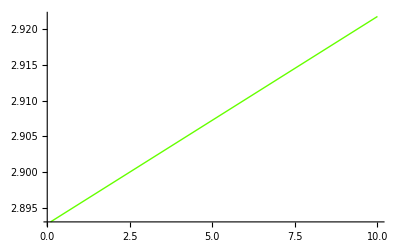
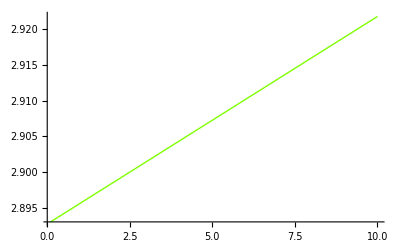
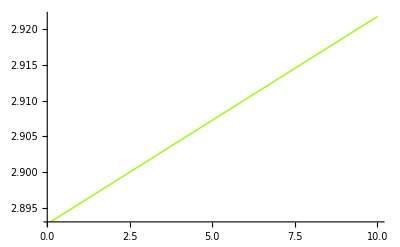
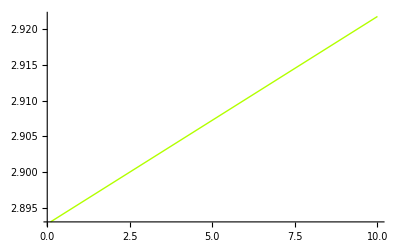
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}[7]

```mathematica
plots
```

```mathematica
(*Our model*)
param = {};
OmegaDE[z_]:=-1+(z+1)*y'[z]/(3*y[z])
CapitalOmegaDE[z_]:=y[z]/(y[z]+(z+1)^3+χ*(z+1)^4)
H[z_]:=Sqrt[ms*(y[z]+(z+1)^3+χ*(z+1)^4)]
Omegatotal[z_]:=(2*(z+1)*H'[z])/(3 H[z])-1
DecParQ[z_]:=-1+(z+1)*H'[z]/H[z]
For[i=1,i<=Length[solyExtended],i++,
AppendTo[param,{Evaluate[CapitalOmegaDE[0]/. solyExtended[[i]]],
Evaluate[OmegaDE[0]/. solyExtended[[i]]],
Evaluate[DecParQ[0]/. solyExtended[[i]]],
Evaluate[H[0]/. solyExtended[[i]]]}]]

MatrixForm[param];
```

```mathematica
(*LCDM*)
LCDMH[z_]:=H0*Sqrt[OmegaL+OmegaM*(z+1)^3+OmegaR*(z+1)^4]
LCDMyh[z_]:=(LCDMH[z]^2)/ms-(1+z)^3-χ*(1+z)^4
LCDMOmegaDE[z_]:=-1+(z+1)/(3*LCDMyh[z])*LCDMyh'[z]
LCDMCapitalOmegaDE[z_]:=LCDMyh[z]/(LCDMyh[z]+(z+1)^3+χ*(z+1)^4)
LCDMOmegatotal[z_]:=(2 (z+1) LCDMH'[z])/(3 LCDMH[z])-1
LCDMDecParQ[z_]:=-1+(z+1)*LCDMH'[z]/LCDMH[z]
Evaluate[LCDMCapitalOmegaDE[0]]
Evaluate[LCDMOmegaDE[0]]
Evaluate[LCDMDecParQ[0]]
Evaluate[LCDMH[0]]
```

0.92684

-0.73751

-0.52532

1.36965×10^-33

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

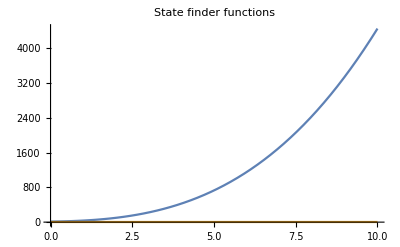

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

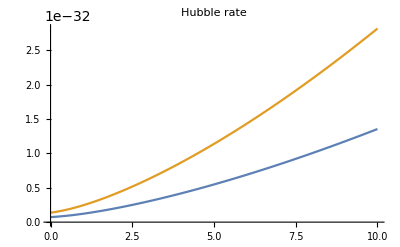

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

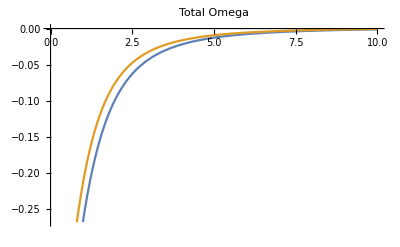

InterpolatingFunction::dmval: Input value {0.000194071} lies outside the range of data in the interpolating function. Extrapolation will be used.

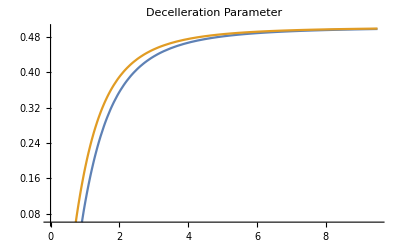

```mathematica
Plot[{LCDMyh[z],y[z] /. soly[[1]]},{z,0,10},PlotLabel->"State finder functions"]
Plot[{H[z]/. soly[[1]],LCDMH[z]},{z,0,10},PlotLabel->"Hubble rate"]
Plot[{Omegatotal[z]/. soly[[1]],LCDMOmegatotal[z]},{z,0,10},PlotLabel->"Total Omega"]
Plot[{DecParQ[z]/. soly[[1]],LCDMDecParQ[z]},{z,0,9.5},PlotLabel->"Decelleration Parameter"]
```

```mathematica
NumberForm[y[10] /.soly[[1]],15]
```

2.92170975430208

```mathematica
(*Saving the interpolating functions. We can import them using the same command as was used with viable*)
```

```mathematica
Export["interpolation2.mx",soly]
Export["intercont2.mx",solyExtended]
```

interpolation2.mx

intercont2.mx

7